# Mathematica Cours 2

```mathematica
Quit[]
```

## Q 1

```mathematica
L={1,1,2,3,5,8,13,21,34}
```

{1,1,2,3,5,8,13,21,34}

```mathematica
L[[5]]
```

5

```mathematica
First[L]
```

1

```mathematica
L//First
```

1

```mathematica
Last[L]
```

34

```mathematica
Length[L]
```

9

## Q 2

```mathematica
L=Prepend[L,b]
```

{b,1,1,2,3,5,8,13,21,34}

```mathematica
L=Append[L,c]
```

{1,1,2,3,5,8,13,21,34,c}

```mathematica
L1=Delete[L,5]
```

{1,1,2,3,8,13,21,34,c}

```mathematica
Range[L]
```

{{1},{1},{1,2},{1,2,3},{1,2,3,4,5},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34},Range[c]}

```mathematica
Table[f[k],{k,1,n}];
```

## Q 3

```mathematica
Clear[L]
```

```mathematica
L={{1,2},{3,4},{2,5}}
```

{{1,2},{3,4},{2,5}}

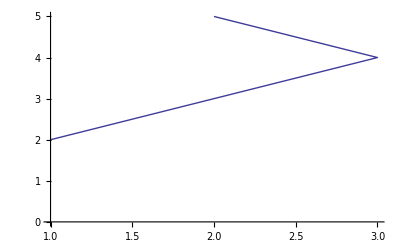

```mathematica
ListPlot[L,PlotJoined->True]
```

## Q 4 :

```mathematica
Clear[L]
```

```mathematica
L={a,b,c}
```

{a,b,c}

```mathematica
f/@L
```

{f[a],f[b],f[c]}

```mathematica
Map[f,L]
```

{f[a],f[b],f[c]}

```mathematica
L2=Table[x^2,{x,3,7}]
```

{9,16,25,36,49}

## Q 5

```mathematica
Clear[L]
```

```mathematica
Clear[f1]
```

```mathematica
f1[k_]:=Exp[2*I*k*Pi/5]
```

```mathematica
f1[1]
```

ⅇ^((2 ⅈ π)/5)

```mathematica
g[z_]:={Re[z],Im[z]}
```

```mathematica
h:=Composition[g,f1]
```

```mathematica
L={h[0],h[1],h[2],h[3],h[4]}
```

{{1,0},{Re[ⅇ^((2 ⅈ π)/5)],Im[ⅇ^((2 ⅈ π)/5)]},{Re[ⅇ^((4 ⅈ π)/5)],Im[ⅇ^((4 ⅈ π)/5)]},{Re[ⅇ^(-(4 ⅈ π)/5)],Im[ⅇ^(-(4 ⅈ π)/5)]},{Re[ⅇ^(-(2 ⅈ π)/5)],Im[ⅇ^(-(2 ⅈ π)/5)]}}

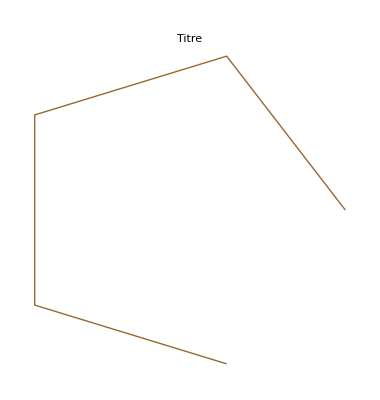

```mathematica
ListPlot[L,PlotJoined->True,
PlotStyle->{Brown},
AspectRatio->Automatic,
Axes->False,
PlotLabel->"Titre"]
```